```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

e1=Take[Import[wd<>"/../../output/e_0.250.dat"]][[All,{1,2,4}]];
e2=Take[Import[wd<>"/../../output/e_1.250.dat"]][[All,{1,2,4}]];
e3=Take[Import[wd<>"/../../output/e_2.250.dat"]][[All,{1,2,4}]];
e4=Take[Import[wd<>"/../../output/e_3.250.dat"]][[All,{1,2,4}]];
(*e5=Take[Import[wd<>"/../../output/e_4.250.dat"]][[All,{1,2,4}]];*)

ux1=Take[Import[wd<>"/../../output/ux_0.250.dat"]][[All,{1,2,4}]];
ux2=Take[Import[wd<>"/../../output/ux_1.250.dat"]][[All,{1,2,4}]];
ux3=Take[Import[wd<>"/../../output/ux_2.250.dat"]][[All,{1,2,4}]];
ux4=Take[Import[wd<>"/../../output/ux_3.250.dat"]][[All,{1,2,4}]];
(*ux5=Take[Import[wd<>"/../../output/ux_4.250.dat"]][[All,{1,2,4}]];*)

ur1=Take[Import[wd<>"/../../output/ur_0.250.dat"]][[All,{1,2,4}]];
ur2=Take[Import[wd<>"/../../output/ur_1.250.dat"]][[All,{1,2,4}]];
ur3=Take[Import[wd<>"/../../output/ur_2.250.dat"]][[All,{1,2,4}]];
ur4=Take[Import[wd<>"/../../output/ur_3.250.dat"]][[All,{1,2,4}]];
```

```mathematica
(*max = 6.0001;*)
max=4.0;

xmin=-5.0;
dx= 0.025;
xpts=401;

s1=1+xpts*(xpts-1)/2;
s2=xpts*(1+(xpts-1)/2);
```

```mathematica
pts=1/dx;

DarkBlueBlueBlend=Table[Blend[{Darker[Blue],Blue},dx*i],{i,0,pts-1}];
BlueCyanBlend=Table[Blend[{Blue,Cyan},dx*i],{i,0,pts-1}];
CyanGreenBlend=Table[Blend[{Cyan,Green},dx*i],{i,0,pts-1}];
GreenYellowBlend=Table[Blend[{Green,Yellow},dx*i],{i,0,pts-1}];
YellowOrangeBlend=Table[Blend[{Yellow,Orange},dx*i],{i,0,pts-1}];
OrangeRedBlend=Table[Blend[{Orange,Red},dx*i],{i,0,pts-1}];
RedDarkRedBlend=Table[Blend[{Red,Darker[Red]},dx*i],{i,0,pts}];

colors=Flatten[{DarkBlueBlueBlend, BlueCyanBlend, CyanGreenBlend, GreenYellowBlend, YellowOrangeBlend, OrangeRedBlend,RedDarkRedBlend}];

colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Energy"]=Function[x,Blend[Transpose[{colorpts,colors}],x ]];
ColorData["Flow"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

BarLegend[{ColorData["Energy"],{0,1}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
```

```mathematica
emax=Max[e1[[1;;All,3]]];

(* Gubser ideal solution *)
τ0=0.25;
T0=0.6*5.067731;
q=1.0;
T0hat=T0*τ0*((1.0+q^2*τ0^2)/(2.0*q*τ0))^(2/3)
(*T0hat=1.2;*)
(*T0hat=1.25645;*)

dof=15.6269;
T[τ_,r_]:=(T0hat*(2.0*q*τ)^(2/3))/(τ(1.0+2.0*q^2(τ^2+r^2)+q^4*(τ^2-r^2)^2)^(1/3));
energy[τ_,r_]:=dof*T[τ,r]^4;
κ[τ_,r_]:=ArcTanh[(2.0*q^2*τ*Abs[r])/(1.0+q^2*(τ^2+r^2))];
ux[τ_,r_]:=Sinh[κ[τ,r]]*Sign[r];


e1test=Table[{xmin +i*dx,energy[0.25,xmin+i*dx]},{i,0,xpts-1}];
e2test=Table[{xmin +i*dx,energy[1.25,xmin+i*dx]},{i,0,xpts-1}];
e3test=Table[{xmin +i*dx,energy[2.25,xmin+i*dx]},{i,0,xpts-1}];
e4test=Table[{xmin +i*dx,energy[3.25,xmin+i*dx]},{i,0,xpts-1}];
e5test=Table[{xmin +i*dx,energy[4.25,xmin+i*dx]},{i,0,xpts-1}];

ux1test=Table[{xmin +i*dx,ux[0.25,xmin+i*dx]},{i,0,xpts-1}];
ux2test=Table[{xmin +i*dx,ux[1.25,xmin+i*dx]},{i,0,xpts-1}];
ux3test=Table[{xmin +i*dx,ux[2.25,xmin+i*dx]},{i,0,xpts-1}];
ux4test=Table[{xmin +i*dx,ux[3.25,xmin+i*dx]},{i,0,xpts-1}];
ux5test=Table[{xmin +i*dx,ux[4.25,xmin+i*dx]},{i,0,xpts-1}];

e1slice=e1[[s1;;s2,{1,3}]];
e2slice=e2[[s1;;s2,{1,3}]];
e3slice=e3[[s1;;s2,{1,3}]];
e4slice=e4[[s1;;s2,{1,3}]];
(*e5slice=e5[[s1;;s2,{1,3}]];*)

ux1slice=ux1[[s1;;s2,{1,3}]];
ux2slice=ux2[[s1;;s2,{1,3}]];
ux3slice=ux3[[s1;;s2,{1,3}]];
ux4slice=ux4[[s1;;s2,{1,3}]];
(*ux5slice=ux5[[s1;;s2,{1,3}]];*)

magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[3.5],Opacity[0.3]};
redTran={Red,AbsoluteThickness[3.5],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[3.5],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[3.5],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[3.5],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[3.5],Opacity[0.3]};
purpleTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[3.5],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
red={Red,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
blue={Blue,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
purple={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};


style={magentaTran,redTran,orangeTran,greenTran,(*cyanTran,blueTran,purpleTran,*)magenta,red,orange,green(*,cyan,blue,purple*)};
```

1.25645

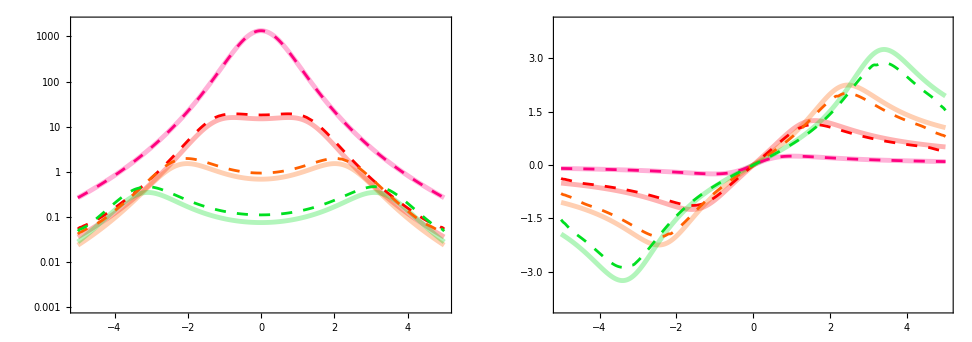

```mathematica
GraphicsGrid[{{
ListLogPlot[{e1test,e2test,e3test,e4test,(*e5test,*)e1slice,e2slice,e3slice,e4slice(*,e5slice*)},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.001,2000}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListPlot[{ux1test,ux2test,ux3test,ux4test,(*ux5test,*)ux1slice,ux2slice,ux3slice,ux4slice(*,ux5slice*)},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{-4,4}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]
}}]

Export[wd<>"/gubser_test_pl_matching.pdf",%];
```

```mathematica
Max[e1[[All,3]]]
Max[e2[[All,3]]]
Max[e3[[All,3]]]
Max[e4[[All,3]]]
```

1335.77

19.31

1.97906

0.511237

```mathematica
plot=Grid[{{ListDensityPlot[e1,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,1350}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e2,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,20}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e3,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,2.00}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e4,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,0.52}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250]},

{ListDensityPlot[ur1,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur2,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur3,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur4,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250]}}];
```

```mathematica
Export[wd<>"/energy.eps",plot];
```